```mathematica
assumptions=β τ>σ && βp τp>σp&&σ==σp&&β>0&& τ>0&&σ>0&&βp>0&&τp>0&&σp>0;
FullSimplify[Reduce[assumptions &&β<βp && β τ<βp τp, PositiveReals]]
```

0<β<βp&&σp>0&&τp>σp/βp&&σp/β<τ<(βp τp)/β&&σ==σp

```mathematica
ClearAll["Global`*"]
Needs["PhysicalConstants`"]
InfoRatio[L_, R_, r_, n_]:=(1/L^(2 n)-1/r^(2 n))/(1/L^(2 n)-1/R^(2 n))
InfoRatio[L_, R_, n_]:=InfoRatio[L, R, α R^n, n]
BetaBound[L_, R_, r_, n_]:=InfoRatio[L, R, r, n] Exp[-(Pi^(n/2) r^(n-1))/(2 Gamma[n/2])]
BetaBound[L_, R_, n_]:=BetaBound[L, R, α R^n, n]
α[ρ_, n_]:=2 ρ Pi^(n/2) GravitationalConstant/(SpeedOfLight^2 Gamma[n/2+1])(Kilogram Meter/(Newton Second^2)) (Kilogram/Meter^n)
```

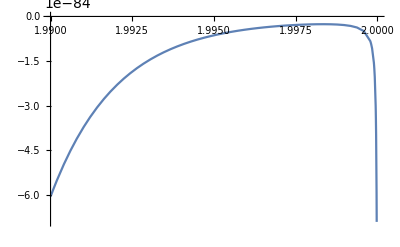

```mathematica
Plot[BetaBound[2, R, 3]/.α->1, {R, 2-1/100, 2}]
```

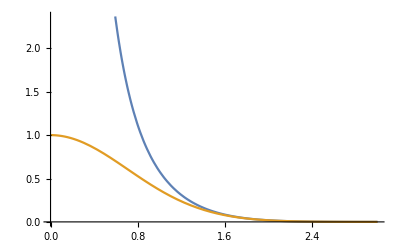

```mathematica
Plot[{1/(Exp[x^2]-1), Exp[-x^2]}, {x, 0, 3}]
```

```mathematica
1/(1-Exp[-x^2])-1
```

-1+1/(1-ⅇ^(-x^2))

```mathematica
Simplify[-1+1/(1-ⅇ^(-x^2))]
```

1/(-1+ⅇ^(x^2))

```mathematica
Series[1/(Exp[x^2]-1), {x, Infinity, 10}]//Normal
```

1/(-1+ⅇ^(x^2))